#### Creating an ambiguous cylinder Written by Evelyn Sander 2019

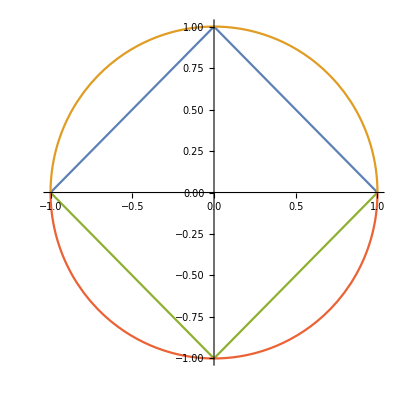

```mathematica
Plot[ {1-Abs[t],Sqrt[1-t^2],-(1-Abs[t]),-Sqrt[1-t^2]},{t,-1,1},AspectRatio->Equal]
```

```mathematica
f1 = 1-Abs[t]
f2 = -(1-Abs[t])
g1 = Sqrt[1-t^2]
g2 = -Sqrt[1-t^2]
```

1-Abs[t]

-1+Abs[t]

√(1-t^2)

-√(1-t^2)

```mathematica
alpha = 1/Sqrt[2]
h = 2
```

1/(√2)

2

```mathematica
sum1 = alpha( f1 + g1)
sum2 = alpha ( f2 + g2)
diff1 = alpha (g1-f1)
diff2 = alpha(g2-f2)
```

(1+√(1-t^2)-Abs[t])/(√2)

(-1-√(1-t^2)+Abs[t])/(√2)

(-1+√(1-t^2)+Abs[t])/(√2)

(1-√(1-t^2)-Abs[t])/(√2)

```mathematica
a = ParametricPlot3D[{{t,sum1, h + diff1},{t,sum2,h+diff2}},{t,-1,1},AspectRatio->Equal,ViewPoint->{0,Infinity,Infinity}]
```

-Graphics3D-

```mathematica
Show[a,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[a,ViewPoint->{0,-Infinity,Infinity}]
```

-Graphics3D-

```mathematica
a3 = ParametricPlot3D[20{ {t,sum1,u (h + diff1)},{t,sum2,u (h+ diff2)}},{u,0,1},{t,-1,1},PlotStyle->Thickness[2],Mesh-> False,PlotPoints->100, AspectRatio->Equal,ViewPoint->{0,Infinity,Infinity}]
```

-Graphics3D-

```mathematica
Show[a3,ViewPoint->Back]
```

-Graphics3D-

```mathematica
Show[a3,ViewPoint->{0,-Infinity,Infinity}]
```

-Graphics3D-

```mathematica
Export["ambiguity.stl",a3]
```

ambiguity.stl